```mathematica
(* combined experiment: extended Fuchsian in 21 dimensions: 3 elliptic ,One flat,and one hyperbolic triangle group*)
```

```mathematica
(* <2,3,3,-6> and <2,3,4,-12> and  <2,3,5,-30>  and  <2,3,6,-36>and <2,3,7,42> together*)
```

```mathematica
(* hyper -Platonic Fuchsian: tetrahedron,cube,dodecahedron, flat 6 and 7th order polyhedron  PSL(2,7)*)
```

```mathematica
Clear[a,b,w]
```

```mathematica
v={2,3,3,-6,2,3,4,-12,2,3,5,-30,2,3,6,-36,2,3,7,42,-36/143}
```

{2,3,3,-6,2,3,4,-12,2,3,5,-30,2,3,6,-36,2,3,7,42,-36/143}

```mathematica
(* Teichmülar space as T[16,5]*)
```

```mathematica
3*(21-5)-3+5
```

50

```mathematica
Length[v]
```

21

```mathematica
Sum[1/v[[i]],{i,Length[v]}]
```

1

```mathematica
(*Solve[179/36-1/a==1,a]*)
```

```mathematica
w=Table[If[v[[i]]<0,v[[i]]*b,v[[i]]*a],{i,21}]
```

{2 a,3 a,3 a,-6 b,2 a,3 a,4 a,-12 b,2 a,3 a,5 a,-30 b,2 a,3 a,6 a,-36 b,2 a,3 a,7 a,42 a,-(36 b)/143}

```mathematica
Reduce[Sum[1/w[[i]],{i,21}]-1==0,{a,b}]
```

-317+60 a≠0&&b==-(257 a)/(-317+60 a)&&a≠0

```mathematica
Solve[b==-(257 a)/(-317+60 a),a]
```

{{a→(317 b)/(257+60 b)}}

```mathematica
s[1]=N[{{-257,0},{60,-317}}/Sqrt[257*317]]
s[2]=N[{{317,0},{60,257}}/Sqrt[257*317]]
```

{{-0.900403,0.},{0.210211,-1.11061}}

{{1.11061,0.},{0.210211,0.900403}}

```mathematica
Table[Det[s[i]],{i,2}]
```

{1.,1.}

```mathematica
Table[N[Tr[s[i]]],{i,2}]
```

{-2.01102,2.01102}

```mathematica
trm=Apply[Times,w]
```

-2303906424422400/143 a^16 b^5

```mathematica
Reduce[trm-1==0,{a,b}]
```

a≠0&&(b==(-143)^(1/5)/(216 70^(2/5) a^(16/5))||b==-143^(1/5)/(216 70^(2/5) a^(16/5))||b==-((-1)^(2/5) 143^(1/5))/(216 70^(2/5) a^(16/5))||b==((-1)^(3/5) 143^(1/5))/(216 70^(2/5) a^(16/5))||b==-((-1)^(4/5) 143^(1/5))/(216 70^(2/5) a^(16/5)))

```mathematica
a≠0&&(b==(-143)^(1/5)/(216 70^(2/5) a^(16/5))||b==-143^(1/5)/(216 70^(2/5) a^(16/5))||b==-((-1)^(2/5) 143^(1/5))/(216 70^(2/5) a^(16/5))||b==((-1)^(3/5) 143^(1/5))/(216 70^(2/5) a^(16/5))||b==-((-1)^(4/5) 143^(1/5))/(216 70^(2/5) a^(16/5)))/.a->4.8032068*10^(-10)
```

b==1.21796×10^27+8.84897×10^26 ⅈ||b==-1.50548×10^27||b==-4.65218×10^26-1.43179×10^27 ⅈ||b==-4.65218×10^26+1.43179×10^27 ⅈ||b==1.21796×10^27-8.84897×10^26 ⅈ

```mathematica
(*http://en.wikipedia.org/wiki/Observable_universe*)
```

```mathematica
1.5054770072857902*^27/(8.8*10^28/2)
```

0.0342154

```mathematica
a≠0&&(b==(-143)^(1/5)/(216 70^(2/5) a^(16/5))||b==-143^(1/5)/(216 70^(2/5) a^(16/5))||b==-((-1)^(2/5) 143^(1/5))/(216 70^(2/5) a^(16/5))||b==((-1)^(3/5) 143^(1/5))/(216 70^(2/5) a^(16/5))||b==-((-1)^(4/5) 143^(1/5))/(216 70^(2/5) a^(16/5)))/.a->2.99792458*10^(10)
```

b==5.50434×10^-37+3.99914×10^-37 ⅈ||b==-6.80374×10^-37||b==-2.10247×10^-37-6.47075×10^-37 ⅈ||b==-2.10247×10^-37+6.47075×10^-37 ⅈ||b==5.50434×10^-37-3.99914×10^-37 ⅈ

```mathematica
c=2.99792458*10^(10);
hbar=1.05457266*10^(-27);
```

```mathematica
(* vacuum mass*)
```

```mathematica
6.803744417219938*^-37/(2*Pi*hbar/c)
```

3.07831

```mathematica
v={a,b}/.NSolve[trm-1==0,{a,b}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(121001 a)/175984-(92291 b)/87992 == 1.

{{-1.45525-0.000615153 ⅈ,0.000556618+0.000403257 ⅈ},{-1.45525+0.000615153 ⅈ,0.000556618-0.000403257 ⅈ},{-1.45408-0.00100048 ⅈ,-0.000211505+0.000655856 ⅈ},{-1.45408+0.00100048 ⅈ,-0.000211505-0.000655856 ⅈ},{-1.45335,-0.000690226},{0.147212,-1.04992},{0.136858-0.0549658 ⅈ,-1.04313+0.0360323 ⅈ},{0.136858+0.0549658 ⅈ,-1.04313-0.0360323 ⅈ},{0.106984-0.102681 ⅈ,-1.02355+0.0673115 ⅈ},{0.106984+0.102681 ⅈ,-1.02355-0.0673115 ⅈ},{0.061102-0.136539 ⅈ,-0.993474+0.0895068 ⅈ},{0.061102+0.136539 ⅈ,-0.993474-0.0895068 ⅈ},{0.00488156-0.151225 ⅈ,-0.956619+0.0991339 ⅈ},{0.00488156+0.151225 ⅈ,-0.956619-0.0991339 ⅈ},{-0.0541099-0.143404 ⅈ,-0.917948+0.0940072 ⅈ},{-0.0541099+0.143404 ⅈ,-0.917948-0.0940072 ⅈ},{-0.106853-0.112569 ⅈ,-0.883373+0.0737936 ⅈ},{-0.106853+0.112569 ⅈ,-0.883373-0.0737936 ⅈ},{-0.14385-0.0620934 ⅈ,-0.85912+0.0407047 ⅈ},{-0.14385+0.0620934 ⅈ,-0.85912-0.0407047 ⅈ},{-0.157238,-0.850343}}

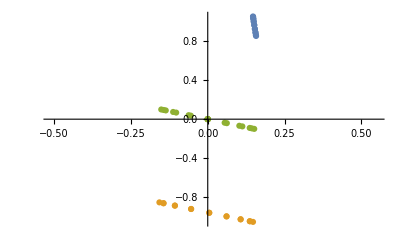

```mathematica
ListPlot[{Abs[v],Re[v],Im[v]}]
```

```mathematica
(* 21  Killing vectors as roots*)
```

```mathematica
ki={Re[a],Im[a],Re[b],Im[b]}/.NSolve[trm-1==0,{a,b}]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(121001 a)/175984-(92291 b)/87992 == 1.

{{-1.45525,-0.000615153,0.000556618,0.000403257},{-1.45525,0.000615153,0.000556618,-0.000403257},{-1.45408,-0.00100048,-0.000211505,0.000655856},{-1.45408,0.00100048,-0.000211505,-0.000655856},{-1.45335,0,-0.000690226,0},{0.147212,0,-1.04992,0},{0.136858,-0.0549658,-1.04313,0.0360323},{0.136858,0.0549658,-1.04313,-0.0360323},{0.106984,-0.102681,-1.02355,0.0673115},{0.106984,0.102681,-1.02355,-0.0673115},{0.061102,-0.136539,-0.993474,0.0895068},{0.061102,0.136539,-0.993474,-0.0895068},{0.00488156,-0.151225,-0.956619,0.0991339},{0.00488156,0.151225,-0.956619,-0.0991339},{-0.0541099,-0.143404,-0.917948,0.0940072},{-0.0541099,0.143404,-0.917948,-0.0940072},{-0.106853,-0.112569,-0.883373,0.0737936},{-0.106853,0.112569,-0.883373,-0.0737936},{-0.14385,-0.0620934,-0.85912,0.0407047},{-0.14385,0.0620934,-0.85912,-0.0407047},{-0.157238,0,-0.850343,0}}

```mathematica
kit=Transpose[ki]
```

{{-1.45525,-1.45525,-1.45408,-1.45408,-1.45335,0.147212,0.136858,0.136858,0.106984,0.106984,0.061102,0.061102,0.00488156,0.00488156,-0.0541099,-0.0541099,-0.106853,-0.106853,-0.14385,-0.14385,-0.157238},{-0.000615153,0.000615153,-0.00100048,0.00100048,0,0,-0.0549658,0.0549658,-0.102681,0.102681,-0.136539,0.136539,-0.151225,0.151225,-0.143404,0.143404,-0.112569,0.112569,-0.0620934,0.0620934,0},{0.000556618,0.000556618,-0.000211505,-0.000211505,-0.000690226,-1.04992,-1.04313,-1.04313,-1.02355,-1.02355,-0.993474,-0.993474,-0.956619,-0.956619,-0.917948,-0.917948,-0.883373,-0.883373,-0.85912,-0.85912,-0.850343},{0.000403257,-0.000403257,0.000655856,-0.000655856,0,0,0.0360323,-0.0360323,0.0673115,-0.0673115,0.0895068,-0.0895068,0.0991339,-0.0991339,0.0940072,-0.0940072,0.0737936,-0.0737936,0.0407047,-0.0407047,0}}

```mathematica
kk1=ki.kit
```

{{2.11775,2.11775,2.11605,2.11605,2.11499,-0.214815,-0.199694,-0.199791,-0.156168,-0.156349,-0.0893516,-0.0895917,-0.00750336,-0.00776937,0.0783586,0.0781064,0.155105,0.154907,0.208913,0.208804,0.228347},{2.11775,2.11775,2.11605,2.11605,2.11499,-0.214815,-0.199791,-0.199694,-0.156349,-0.156168,-0.0895917,-0.0893516,-0.00776937,-0.00750336,0.0781064,0.0783586,0.154907,0.155105,0.208804,0.208913,0.228347},{2.11605,2.11605,2.11435,2.11434,2.11328,-0.213836,-0.198702,-0.19886,-0.1552,-0.155494,-0.0884416,-0.0888323,-0.00667953,-0.00711216,0.0790793,0.0786691,0.155721,0.155398,0.209439,0.209261,0.228816},{2.11605,2.11605,2.11434,2.11435,2.11328,-0.213836,-0.19886,-0.198702,-0.155494,-0.1552,-0.0888323,-0.0884416,-0.00711216,-0.00667953,0.0786691,0.0790793,0.155398,0.155721,0.209261,0.209439,0.228816},{2.11499,2.11499,2.11328,2.11328,2.11222,-0.213225,-0.198182,-0.198182,-0.154779,-0.154779,-0.0881167,-0.0881167,-0.00643433,-0.00643433,0.0792741,0.0792741,0.155904,0.155904,0.209656,0.209656,0.229108},{-0.214815,-0.214815,-0.213836,-0.213836,-0.213225,1.12401,1.11536,1.11536,1.0904,1.0904,1.05207,1.05207,1.00509,1.00509,0.955808,0.955808,0.911743,0.911743,0.880833,0.880833,0.869647},{-0.199694,-0.199791,-0.198702,-0.19886,-0.198182,1.11536,1.11118,1.10254,1.09041,1.07427,1.05542,1.03396,1.01044,0.986667,0.961408,0.938868,0.915699,0.898007,0.881371,0.871611,0.865504},{-0.199791,-0.199694,-0.19886,-0.198702,-0.198182,1.11536,1.10254,1.11118,1.07427,1.09041,1.03396,1.05542,0.986667,1.01044,0.938868,0.961408,0.898007,0.915699,0.871611,0.881371,0.865504},{-0.156168,-0.156349,-0.1552,-0.155494,-0.154779,1.0904,1.09041,1.07427,1.07418,1.04403,1.04345,1.00336,1.00187,0.95747,0.954831,0.912725,0.909272,0.87622,0.87308,0.854848,0.853548},{-0.156349,-0.156168,-0.155494,-0.1552,-0.154779,1.0904,1.07427,1.09041,1.04403,1.07418,1.00336,1.04345,0.95747,1.00187,0.912725,0.954831,0.87622,0.909272,0.854848,0.87308,0.853548},{-0.0893516,-0.0895917,-0.0884416,-0.0888323,-0.0881167,1.05207,1.05542,1.03396,1.04345,1.00336,1.01738,0.96407,0.980196,0.921153,0.936646,0.880656,0.893054,0.849104,0.856845,0.832602,0.835187},{-0.0895917,-0.0893516,-0.0888323,-0.0884416,-0.0881167,1.05207,1.03396,1.05542,1.00336,1.04345,0.96407,1.01738,0.921153,0.980196,0.880656,0.936646,0.849104,0.893054,0.832602,0.856845,0.835187},{-0.00750336,-0.00776937,-0.00667953,-0.00711216,-0.00643433,1.00509,1.01044,0.986667,1.00187,0.95747,0.980196,0.921153,0.94784,0.882448,0.908868,0.846857,0.868868,0.820191,0.834574,0.807723,0.812687},{-0.00776937,-0.00750336,-0.00711216,-0.00667953,-0.00643433,1.00509,0.986667,1.01044,0.95747,1.00187,0.921153,0.980196,0.882448,0.94784,0.846857,0.908868,0.820191,0.868868,0.807723,0.834574,0.812687},{0.0783586,0.0781064,0.0790793,0.0786691,0.0792741,0.955808,0.961408,0.938868,0.954831,0.912725,0.936646,0.880656,0.908868,0.846857,0.874958,0.816154,0.839752,0.793592,0.809142,0.78368,0.789079},{0.0781064,0.0783586,0.0786691,0.0790793,0.0792741,0.955808,0.938868,0.961408,0.912725,0.954831,0.880656,0.936646,0.846857,0.908868,0.816154,0.874958,0.793592,0.839752,0.78368,0.809142,0.789079},{0.155105,0.154907,0.155721,0.155398,0.155904,0.911743,0.915699,0.898007,0.909272,0.87622,0.893054,0.849104,0.868868,0.820191,0.839752,0.793592,0.809882,0.773647,0.784287,0.7643,0.767971},{0.154907,0.155105,0.155398,0.155721,0.155904,0.911743,0.898007,0.915699,0.87622,0.909272,0.849104,0.893054,0.820191,0.868868,0.793592,0.839752,0.773647,0.809882,0.7643,0.784287,0.767971},{0.208913,0.208804,0.209439,0.209261,0.209656,0.880833,0.881371,0.871611,0.87308,0.854848,0.856845,0.832602,0.834574,0.807723,0.809142,0.78368,0.784287,0.7643,0.764292,0.753267,0.753166},{0.208804,0.208913,0.209261,0.209439,0.209656,0.880833,0.871611,0.881371,0.854848,0.87308,0.832602,0.856845,0.807723,0.834574,0.78368,0.809142,0.7643,0.784287,0.753267,0.764292,0.753166},{0.228347,0.228347,0.228816,0.228816,0.229108,0.869647,0.865504,0.865504,0.853548,0.853548,0.835187,0.835187,0.812687,0.812687,0.789079,0.789079,0.767971,0.767971,0.753166,0.753166,0.747808}}

```mathematica
Eigenvalues[kk1]//Chop
```

{14.6271,10.757,0.263557,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
kk2=kit.ki
```

{{10.7608,0.,-0.120842,0.},{0.,0.18434,0.,-0.120842},{-0.120842,0.,14.6233,0.},{0.,-0.120842,0.,0.079217}}

```mathematica
Eigenvalues[kk2]//Chop
```

{14.6271,10.757,0.263557,0}

```mathematica
(* 21x21 Cartan matrix*)
```

```mathematica
ca=Table[2*ki[[i]].ki[[j]]/(ki[[i]].ki[[i]]),{i,Length[ki]},{j,Length[ki]}]
```

{{2.,2.,1.99839,1.99839,1.99738,-0.20287,-0.188591,-0.188682,-0.147485,-0.147655,-0.0843833,-0.0846101,-0.00708615,-0.00733737,0.0740016,0.0737634,0.146481,0.146294,0.197297,0.197194,0.21565},{2.,2.,1.99839,1.99839,1.99738,-0.20287,-0.188682,-0.188591,-0.147655,-0.147485,-0.0846101,-0.0843833,-0.00733737,-0.00708615,0.0737634,0.0740016,0.146294,0.146481,0.197194,0.197297,0.21565},{2.00161,2.00161,2.,2.,1.99899,-0.202271,-0.187956,-0.188105,-0.146807,-0.147084,-0.0836586,-0.0840281,-0.0063183,-0.00672753,0.0748026,0.0744146,0.147299,0.146994,0.198112,0.197944,0.216441},{2.00161,2.00161,2.,2.,1.99899,-0.202271,-0.188105,-0.187956,-0.147084,-0.146807,-0.0840281,-0.0836586,-0.00672753,-0.0063183,0.0744146,0.0748026,0.146994,0.147299,0.197944,0.198112,0.216441},{2.00262,2.00262,2.001,2.001,2.,-0.201897,-0.187652,-0.187652,-0.146555,-0.146555,-0.0834351,-0.0834351,-0.00609247,-0.00609247,0.0750623,0.0750623,0.147621,0.147621,0.198517,0.198517,0.216935},{-0.382229,-0.382229,-0.380487,-0.380487,-0.379402,2.,1.98461,1.98461,1.9402,1.9402,1.87199,1.87199,1.78841,1.78841,1.70071,1.70071,1.62231,1.62231,1.56731,1.56731,1.5474},{-0.359428,-0.359602,-0.357642,-0.357925,-0.356705,2.00752,2.,1.98445,1.96262,1.93357,1.89964,1.86101,1.81867,1.77589,1.73043,1.68986,1.64816,1.61631,1.58637,1.5688,1.55781},{-0.359602,-0.359428,-0.357925,-0.357642,-0.356705,2.00752,1.98445,2.,1.93357,1.96262,1.86101,1.89964,1.77589,1.81867,1.68986,1.73043,1.61631,1.64816,1.5688,1.58637,1.55781},{-0.290768,-0.291104,-0.288965,-0.289512,-0.288181,2.0302,2.03023,2.00018,2.,1.94387,1.9428,1.86815,1.86538,1.7827,1.77779,1.69939,1.69296,1.63142,1.62558,1.59163,1.58921},{-0.291104,-0.290768,-0.289512,-0.288965,-0.288181,2.0302,2.00018,2.03023,1.94387,2.,1.86815,1.9428,1.7827,1.86538,1.69939,1.77779,1.63142,1.69296,1.59163,1.62558,1.58921},{-0.175651,-0.176123,-0.173862,-0.17463,-0.173223,2.06819,2.07478,2.0326,2.05126,1.97245,2.,1.8952,1.92691,1.81084,1.84129,1.73123,1.7556,1.6692,1.68442,1.63676,1.64184},{-0.176123,-0.175651,-0.17463,-0.173862,-0.173223,2.06819,2.0326,2.07478,1.97245,2.05126,1.8952,2.,1.81084,1.92691,1.73123,1.84129,1.6692,1.7556,1.63676,1.68442,1.64184},{-0.0158325,-0.0163938,-0.0140942,-0.0150071,-0.0135768,2.12081,2.13208,2.08193,2.11401,2.02032,2.06827,1.94369,2.,1.86202,1.91777,1.78692,1.83336,1.73065,1.761,1.70434,1.71482},{-0.0163938,-0.0158325,-0.0150071,-0.0140942,-0.0135768,2.12081,2.08193,2.13208,2.02032,2.11401,1.94369,2.06827,1.86202,2.,1.78692,1.91777,1.73065,1.83336,1.70434,1.761,1.71482},{0.179114,0.178537,0.180761,0.179824,0.181207,2.18481,2.19761,2.14609,2.18257,2.08633,2.14101,2.01303,2.07751,1.93577,2.,1.86558,1.91952,1.81401,1.84956,1.79135,1.8037},{0.178537,0.179114,0.179824,0.180761,0.181207,2.18481,2.14609,2.19761,2.08633,2.18257,2.01303,2.14101,1.93577,2.07751,1.86558,2.,1.81401,1.91952,1.79135,1.84956,1.8037},{0.383032,0.382543,0.384551,0.383756,0.385005,2.25154,2.26132,2.21762,2.24544,2.16382,2.20539,2.09686,2.14567,2.02546,2.07376,1.95977,2.,1.91052,1.93679,1.88744,1.8965},{0.382543,0.383032,0.383756,0.384551,0.385005,2.25154,2.21762,2.26132,2.16382,2.24544,2.09686,2.20539,2.02546,2.14567,1.95977,2.07376,1.91052,2.,1.88744,1.93679,1.8965},{0.546685,0.546399,0.54806,0.547595,0.548629,2.30496,2.30637,2.28083,2.28467,2.23697,2.24219,2.17875,2.18391,2.11365,2.11736,2.05073,2.05232,2.00002,2.,1.97115,1.97088},{0.546399,0.546685,0.547595,0.54806,0.548629,2.30496,2.28083,2.30637,2.23697,2.28467,2.17875,2.24219,2.11365,2.18391,2.05073,2.11736,2.00002,2.05232,1.97115,2.,1.97088},{0.61071,0.61071,0.611964,0.611964,0.612745,2.32586,2.31478,2.31478,2.2828,2.2828,2.23369,2.23369,2.17352,2.17352,2.11038,2.11038,2.05393,2.05393,2.01433,2.01433,2.}}

```mathematica
AdjacencyGraph[Round[ca]]
```

-Graphics-

```mathematica
(*2nd 4x4 Cartan Matrix*)
```

```mathematica
ca2=Table[2*kit[[i]].kit[[j]]/(kit[[i]].kit[[i]]),{i,Length[kit]},{j,Length[kit]}]
```

{{2.,0.,-0.0224598,0.},{0.,2.,0.,-1.31108},{-0.0165273,0.,2.,0.},{0.,-3.05092,0.,2.}}

```mathematica
TableForm[ca2]
```

2. | 0. | -0.0224598 | 0.
0. | 2. | 0. | -1.31108
-0.0165273 | 0. | 2. | 0.
0. | -3.05092 | 0. | 2.

```mathematica
WeightedAdjacencyGraph[ca2]
```

-Graphics-

```mathematica
TableForm[ca]
```

2. | 2. | 1.99839 | 1.99839 | 1.99738 | -0.20287 | -0.188591 | -0.188682 | -0.147485 | -0.147655 | -0.0843833 | -0.0846101 | -0.00708615 | -0.00733737 | 0.0740016 | 0.0737634 | 0.146481 | 0.146294 | 0.197297 | 0.197194 | 0.21565
2. | 2. | 1.99839 | 1.99839 | 1.99738 | -0.20287 | -0.188682 | -0.188591 | -0.147655 | -0.147485 | -0.0846101 | -0.0843833 | -0.00733737 | -0.00708615 | 0.0737634 | 0.0740016 | 0.146294 | 0.146481 | 0.197194 | 0.197297 | 0.21565
2.00161 | 2.00161 | 2. | 2. | 1.99899 | -0.202271 | -0.187956 | -0.188105 | -0.146807 | -0.147084 | -0.0836586 | -0.0840281 | -0.0063183 | -0.00672753 | 0.0748026 | 0.0744146 | 0.147299 | 0.146994 | 0.198112 | 0.197944 | 0.216441
2.00161 | 2.00161 | 2. | 2. | 1.99899 | -0.202271 | -0.188105 | -0.187956 | -0.147084 | -0.146807 | -0.0840281 | -0.0836586 | -0.00672753 | -0.0063183 | 0.0744146 | 0.0748026 | 0.146994 | 0.147299 | 0.197944 | 0.198112 | 0.216441
2.00262 | 2.00262 | 2.001 | 2.001 | 2. | -0.201897 | -0.187652 | -0.187652 | -0.146555 | -0.146555 | -0.0834351 | -0.0834351 | -0.00609247 | -0.00609247 | 0.0750623 | 0.0750623 | 0.147621 | 0.147621 | 0.198517 | 0.198517 | 0.216935
-0.382229 | -0.382229 | -0.380487 | -0.380487 | -0.379402 | 2. | 1.98461 | 1.98461 | 1.9402 | 1.9402 | 1.87199 | 1.87199 | 1.78841 | 1.78841 | 1.70071 | 1.70071 | 1.62231 | 1.62231 | 1.56731 | 1.56731 | 1.5474
-0.359428 | -0.359602 | -0.357642 | -0.357925 | -0.356705 | 2.00752 | 2. | 1.98445 | 1.96262 | 1.93357 | 1.89964 | 1.86101 | 1.81867 | 1.77589 | 1.73043 | 1.68986 | 1.64816 | 1.61631 | 1.58637 | 1.5688 | 1.55781
-0.359602 | -0.359428 | -0.357925 | -0.357642 | -0.356705 | 2.00752 | 1.98445 | 2. | 1.93357 | 1.96262 | 1.86101 | 1.89964 | 1.77589 | 1.81867 | 1.68986 | 1.73043 | 1.61631 | 1.64816 | 1.5688 | 1.58637 | 1.55781
-0.290768 | -0.291104 | -0.288965 | -0.289512 | -0.288181 | 2.0302 | 2.03023 | 2.00018 | 2. | 1.94387 | 1.9428 | 1.86815 | 1.86538 | 1.7827 | 1.77779 | 1.69939 | 1.69296 | 1.63142 | 1.62558 | 1.59163 | 1.58921
-0.291104 | -0.290768 | -0.289512 | -0.288965 | -0.288181 | 2.0302 | 2.00018 | 2.03023 | 1.94387 | 2. | 1.86815 | 1.9428 | 1.7827 | 1.86538 | 1.69939 | 1.77779 | 1.63142 | 1.69296 | 1.59163 | 1.62558 | 1.58921
-0.175651 | -0.176123 | -0.173862 | -0.17463 | -0.173223 | 2.06819 | 2.07478 | 2.0326 | 2.05126 | 1.97245 | 2. | 1.8952 | 1.92691 | 1.81084 | 1.84129 | 1.73123 | 1.7556 | 1.6692 | 1.68442 | 1.63676 | 1.64184
-0.176123 | -0.175651 | -0.17463 | -0.173862 | -0.173223 | 2.06819 | 2.0326 | 2.07478 | 1.97245 | 2.05126 | 1.8952 | 2. | 1.81084 | 1.92691 | 1.73123 | 1.84129 | 1.6692 | 1.7556 | 1.63676 | 1.68442 | 1.64184
-0.0158325 | -0.0163938 | -0.0140942 | -0.0150071 | -0.0135768 | 2.12081 | 2.13208 | 2.08193 | 2.11401 | 2.02032 | 2.06827 | 1.94369 | 2. | 1.86202 | 1.91777 | 1.78692 | 1.83336 | 1.73065 | 1.761 | 1.70434 | 1.71482
-0.0163938 | -0.0158325 | -0.0150071 | -0.0140942 | -0.0135768 | 2.12081 | 2.08193 | 2.13208 | 2.02032 | 2.11401 | 1.94369 | 2.06827 | 1.86202 | 2. | 1.78692 | 1.91777 | 1.73065 | 1.83336 | 1.70434 | 1.761 | 1.71482
0.179114 | 0.178537 | 0.180761 | 0.179824 | 0.181207 | 2.18481 | 2.19761 | 2.14609 | 2.18257 | 2.08633 | 2.14101 | 2.01303 | 2.07751 | 1.93577 | 2. | 1.86558 | 1.91952 | 1.81401 | 1.84956 | 1.79135 | 1.8037
0.178537 | 0.179114 | 0.179824 | 0.180761 | 0.181207 | 2.18481 | 2.14609 | 2.19761 | 2.08633 | 2.18257 | 2.01303 | 2.14101 | 1.93577 | 2.07751 | 1.86558 | 2. | 1.81401 | 1.91952 | 1.79135 | 1.84956 | 1.8037
0.383032 | 0.382543 | 0.384551 | 0.383756 | 0.385005 | 2.25154 | 2.26132 | 2.21762 | 2.24544 | 2.16382 | 2.20539 | 2.09686 | 2.14567 | 2.02546 | 2.07376 | 1.95977 | 2. | 1.91052 | 1.93679 | 1.88744 | 1.8965
0.382543 | 0.383032 | 0.383756 | 0.384551 | 0.385005 | 2.25154 | 2.21762 | 2.26132 | 2.16382 | 2.24544 | 2.09686 | 2.20539 | 2.02546 | 2.14567 | 1.95977 | 2.07376 | 1.91052 | 2. | 1.88744 | 1.93679 | 1.8965
0.546685 | 0.546399 | 0.54806 | 0.547595 | 0.548629 | 2.30496 | 2.30637 | 2.28083 | 2.28467 | 2.23697 | 2.24219 | 2.17875 | 2.18391 | 2.11365 | 2.11736 | 2.05073 | 2.05232 | 2.00002 | 2. | 1.97115 | 1.97088
0.546399 | 0.546685 | 0.547595 | 0.54806 | 0.548629 | 2.30496 | 2.28083 | 2.30637 | 2.23697 | 2.28467 | 2.17875 | 2.24219 | 2.11365 | 2.18391 | 2.05073 | 2.11736 | 2.00002 | 2.05232 | 1.97115 | 2. | 1.97088
0.61071 | 0.61071 | 0.611964 | 0.611964 | 0.612745 | 2.32586 | 2.31478 | 2.31478 | 2.2828 | 2.2828 | 2.23369 | 2.23369 | 2.17352 | 2.17352 | 2.11038 | 2.11038 | 2.05393 | 2.05393 | 2.01433 | 2.01433 | 2.

```mathematica
Eigenvalues[ca]//Chop
```

{31.0281,10.4047,0.567212,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Tr[ca]
```

42.

```mathematica
Det[ca]//Chop
```

0

```mathematica
p[x_]=Expand[CharacteristicPolynomial[ca,x]/x^18//Chop]
```

183.118-346.34 x+42. x^2-x^3

```mathematica
Discriminant[p[x],x]
```

3.8192×10^7

```mathematica
WeightedAdjacencyGraph[ca]
```

-Graphics-

```mathematica
(*end*)
```

```mathematica
(* Mathematica*)
Clear[cr,cols,cr2,cr3,cr4,p,p0,q0,r0,s0,s,v]
allColors=ColorData["Legacy"][[3,1]];
firstCols={ "Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","White","AliceBlue","LightBlue" ,"Cyan","ManganeseBlue","DodgerBlue" ,"Blue","Magenta","Purple","Pink","Tomato","Red","DarkOrange","Orange","DeepNaplesYellow","Gold","Banana","Yellow","LightYellow","Orange","Pink","LightPink","Yellow","LightYellow","LightPink","White","DeepNaplesYellow", "Orange","DarkOrange","Tomato","Red","Tomato","Pink","LightPink","DeepNaplesYellow", "Orange","DarkOrange","Tomato","White","Pink","Banana","LightBlue","DodgerBlue","Cyan","White","Purple","DarkOrchid","Magenta","ManganeseBlue","DeepNaplesYellow", "Orange","DarkOrange","Tomato","GoldOchre","LightPink","Magenta","Green","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","Yellow","Tomato","DeepNaplesYellow","DodgerBlue","Cyan","Red","Blue","DeepNaplesYellow","Green","Magenta","DarkOrchid","LightSalmon","LightPink","Sienna","Green","Mint","DarkSlateGray","ManganeseBlue","SlateGray","DarkOrange","MistyRose","DeepNaplesYellow","GoldOchre","SapGreen","Yellow","LimeGreen"};
cols=ColorData["Legacy",#]&/@Join[firstCols,Complement[allColors,firstCols]];
rotate[theta_]:={{Cos[theta],-Sin[theta]},{Sin[theta],Cos[theta]}};
cr[n_]:=cr[n]=cols[[n]];
cr2[n_]:=cr2[n]=cols[[n+8]];
cr3[n_]:=cr3[n]=cols[[n+16]];
cr4[n_]:=cr4[n]=cols[[n+24]];
cr5[n_]:=cr5[n]=cols[[n+36]]
```

```mathematica
mu=4.0
```

4.

```mathematica
s[1]=N[{{-257,0},{60,-317}}/Sqrt[257*317]]
s[2]=N[{{317,0},{60,257}}/Sqrt[257*317]]
s[3]={{1+mu*I,mu},{mu,1-mu*I}}
s[4]=Inverse[s[1]]
s[5]=Inverse[s[2]]
s[6]=Inverse[s[3]]
s[7]={{1,0},{0,1}}
s[8]=Inverse[s[7]]
```

{{-0.900403,0.},{0.210211,-1.11061}}

{{1.11061,0.},{0.210211,0.900403}}

{{1.+4. ⅈ,4.},{4.,1.-4. ⅈ}}

{{-1.11061,0.},{-0.210211,-0.900403}}

{{0.900403,0.},{-0.210211,1.11061}}

{{1.-4. ⅈ,-4.+0. ⅈ},{-4.+0. ⅈ,1.+4. ⅈ}}

{{1,0},{0,1}}

{{1,0},{0,1}}

```mathematica
Table[Det[s[i]],{i,8}]//Chop

Table[Tr[s[i]],{i,8}]//Chop
Sum[s[i].s[i],{i,8}]//Chop
```

{1.,1.,1.,1.,1.,1.,1,1}

{-2.01102,2.01102,2.,-2.01102,2.01102,2.,2,2}

{{8.08838,0},{0,8.08838}}

```mathematica
(* the Möbius transforms : Kleinian group in SL(2,c)*)
```

```mathematica
s0=N[{{1,-I},{-I,1}}/Sqrt[2]];s1=Inverse[s0];
qf=N[rotate[Pi/4]];qfi=Inverse[qf];
{a,b,c,d,A0,B0,C0,D0}=Table[N[s[i]],{i,8}]
```

{{{-0.900403,0.},{0.210211,-1.11061}},{{1.11061,0.},{0.210211,0.900403}},{{1.+4. ⅈ,4.},{4.,1.-4. ⅈ}},{{-1.11061,0.},{-0.210211,-0.900403}},{{0.900403,0.},{-0.210211,1.11061}},{{1.-4. ⅈ,-4.+0. ⅈ},{-4.+0. ⅈ,1.+4. ⅈ}},{{1.,0.},{0.,1.}},{{1.,0.},{0.,1.}}}

```mathematica
Det[a]
Tr[a]
Det[b]
Tr[b]
Det[A0]
Tr[A0]
Det[B0]
Tr[B0]
```

1.

-2.01102

1.

2.01102

1.

2.01102

1.+0. ⅈ

2.+0. ⅈ

```mathematica
Affine[{z1_,z2_}]:=0.00001 Round[(z1/z2)/0.00001];
Children[{z_,n_}]:={Affine[{a,b,c,d,A0,B0,C0,D0}[[#]].{z,1}],#}&/@Delete[Range[8],{5,6,7,8,1,2,3,4}[[n]]];
aa1={Re[#[[1]]],Im[#[[1]]]}&/@Nest[Union[Flatten[Children/@#,1]]&,ParallelTable[{Affine[{a,b,c,d,A0,B0,C0,D0}[[i]].{0,1}],i},{i,1,8}],10];
ll=Length[aa1]
Last[aa1]
aa=Delete[Union[aa1],1];
```

653653

{10.8604,-0.08523}

```mathematica
g0=Rasterize[ListPlot[aa,AspectRatio->Automatic,PlotStyle->PointSize[0.001],ImageSize->2000,PlotRange->{{-1.5,1.5},{-0.5,2.5}},ColorFunction-> (Hue[3*#]&)],RasterSize->2000,ImageSize->2000];
```

```mathematica
dlst=ParallelTable[Mod[1+Floor[1+(1+Floor[18*Norm[aa[[i]]]])/(Abs[Cos[Arg[aa[[i,1]]+I*aa[[i,2]]]]]+Abs[Sin[Arg[aa[[i,1]]+I*aa[[i,2]]]]])],Length[cols]],{i,Length[aa]}];
Min[dlst];
Max[dlst];
ptlst=Point[Developer`ToPackedArray[aa],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g2=Rasterize[Graphics[{PointSize[.001],ptlst},AspectRatio->Automatic,ImageSize->2000,PlotRange->{{-1.5,1.5},{-0.5,2.5}},Background->Black],RasterSize->2000,ImageSize->2000];
```

```mathematica
(* end limit set*)
```

```mathematica
(* Half plane to disk conformal map*)

bb1=Delete[Union[ParallelTable[{-(Im[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+2 Re[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]),-2 Im[aa⟦i,2⟧/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]+Re[-1/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,1⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)+aa⟦i,2⟧^2/((1+aa⟦i,1⟧)^2+aa⟦i,2⟧^2)]},{i,Length[aa]}]],Length[aa]];
```

```mathematica
(*ListPlot[bb1,PlotStyle->{{Magenta,PointSize[0.001]},{Purple,PointSize[0.001]}},ImageSize->1000,Axes->True,PlotRange->All]*)
```

```mathematica
ptlst3:=Point[Developer`ToPackedArray[bb1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g3=Rasterize[Graphics[{PointSize[.001],ptlst3(*,ptlst2*)},AspectRatio->Automatic,ImageSize->2000,Background->Black,PlotRange->{{-5,5},{-5,5}}*3/5],RasterSize->2000,ImageSize->2000];
```

```mathematica
(* Sphere conformal map*)

cc1=ParallelTable[{2*aa[[i,1]],2*aa[[i,2]],(1-aa[[i]].aa[[i]])}/(1+aa[[i]].aa[[i]]),{i,Length[aa]}];
```

```mathematica
ptlst5a=Point[Developer`ToPackedArray[cc1],VertexColors->Developer`ToPackedArray[cr/@dlst]];
```

```mathematica
g4=Rasterize[Graphics3D[{PointSize[.001],ptlst5a},AspectRatio->Automatic,ImageSize->2000,PlotRange->All,Background->Black,Boxed->False],RasterSize->2000,ImageSize->2000];
```

```mathematica
Export["Nylander_2group_extended_Fuchsian_233_234_235_236_237_21d_On_disk_scale4_8Limitset_10_Rasterize.jpg",{g0,g2,g3,g4}]
```

Nylander_2group_extended_Fuchsian_233_234_235_236_237_21d_On_disk_scale4_8Limitset_10_Rasterize.jpg

```mathematica
(*end*)
```